## Load the data

Select the parameter (.prm) file of the desired chromatogram. It is assumed that the chromatography files are in the same directory as the parameter file.

```mathematica
SystemDialogInput["FileOpen" , {"C:/Users/fskdm/Dropbox", {"Parameter Files"->{"*.prm"}}}]
```

```mathematica
pfile ="C:\\Users\\fskdm\\My PhD\\Projects\\2019_12_20_PhD_Last_Project\\2019_12_23_PAH_FAMEs\\Chromatograms\\RawData\\2020_02_29-184604.dat.prm"
```

C:\Users\fskdm\My PhD\Projects\2019_12_20_PhD_Last_Project\2019_12_23_PAH_FAMEs\Chromatograms\RawData\2020_02_29-184604.dat.prm

```mathematica
(*Extract the data directory:*)
filedir = FileNameJoin[ FileNameSplit[pfile][[1;;-2]]];

(*Import the parameters:*)
params = Import[pfile, "Lines"];

(*Create the data filename*)
file= FileNameJoin[
		{filedir
	,	FileNameSplit[
		StringSplit[                         
			params[[15]]                    (* Line 15 of the paramaters file contains the name of the data file *)
		][[3]]]                                        (* It is the third part of the line as separated by whitespace *)
		[[-1]]                                                 (* Select the last item on the list of the stringsplit *)
		}
	];(* Extract the filename *)
(* Show the result *)
Framed[TabView[{"Data"-> TableForm[{filedir, file}], "Parameters" -> params}]]
```

12

```mathematica
FrontEndTokenExecute["SaveRename", {StringJoin[file,".nb"]}]
```

```mathematica
data=BinaryReadList[file, {"Integer8"}~Join~Table["Real64", {17}], ByteOrdering->-$ByteOrdering];
```

```mathematica
Length[data[[1]]]
```

18

```mathematica
data[[-5;;-1]]//TableForm
```

2 | 12.232 | 306.841 | 294.102 | 5.14438 | 5.43423 | 2.03828×10^7 | -358756. | 644.62 | 648.527 | -0.0227173 | 627.968 | -0.0970551 | 2.0265×10^7 | 2.76769×10^7 | 673.15 | 673.15 | 623.15
2 | 12.256 | 306.787 | 294.139 | 5.13448 | 5.42655 | 2.04068×10^7 | -395090. | 644.595 | 648.313 | -0.0246552 | 628.511 | -0.0939148 | 2.0265×10^7 | 2.76769×10^7 | 673.15 | 673.15 | 623.15
2 | 12.278 | 306.766 | 294.156 | 5.13177 | 5.42366 | 2.03781×10^7 | -395461. | 644.638 | 648.447 | -0.0298981 | 628.506 | -0.0952148 | 2.0265×10^7 | 2.76769×10^7 | 673.15 | 673.15 | 623.15
3 | 4803.4 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
4 | 4803.4 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.

```mathematica
data[[1;;5]]//TableForm
```

0 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
1 | 2220. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
2 | 0.057 | 305.357 | 293.498 | 2.08824 | 1.22881 | 2.02133×10^7 | 144591. | 505.709 | 508.916 | 0.0175323 | 226.334 | -0.0491913 | 2.0265×10^7 | 2.76769×10^7 | 673.15 | 673.15 | 243.15
2 | 0.079 | 305.35 | 293.51 | 2.08906 | 1.22952 | 2.02162×10^7 | 143292. | 505.976 | 509.142 | 0.0182129 | 226.334 | -0.049469 | 2.0265×10^7 | 2.76769×10^7 | 673.15 | 673.15 | 243.15
2 | 0.13 | 305.344 | 293.474 | 2.13322 | 1.2552 | 2.02125×10^7 | 136242. | 506.009 | 509.112 | 0.0187531 | 226.334 | -0.0490143 | 2.0265×10^7 | 2.76769×10^7 | 673.15 | 673.15 | 256.35

## Investigate manifold Temperatures

Plot the manifold temperatures:

```mathematica
ListPlot[{data[[All,9]]-273.12, data[[All, 10]]- 273.12,data[[All, 16]]- 273.12,data[[All,17]]- 273.12}
, PlotRange->Automatic
(*, PlotLegends->{"Inlet","Detector","Setpoint I","Setpoint D"} *)
, PlotLegends->SwatchLegend[{"Inlet","Detector","Setpoint I","Setpoint D"} ,LegendLabel->"Legend",LegendFunction->(Framed[#,Background->LightBlue]&)]
, AxesLabel->{"Sample","Manfold Temperature (°C)"}
, ImageSize->Large
,PlotLabel->"Reported Manifold temperatures"

]
```

-Graphics-

Just plot the temperatures:

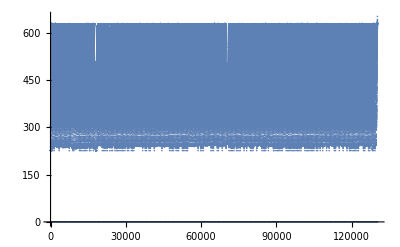

```mathematica
ListPlot[data[[All,12]]]
```

## What are we investigating:

```mathematica
values={"ID", "Time", "TAmbient", "Ttc", "Vb", "dV", "P1", "P2", "TInlet", "TOutlet", "Detector", "TColumn", "Vcol","P1 Setpoint", "P2 Setpoint", "TInlet Setpoint", "TOutlet Setpoint", "TColumn Setpoint"}
```

{ID,Time,TAmbient,Ttc,Vb,dV,P1,P2,TInlet,TOutlet,Detector,TColumn,Vcol,P1 Setpoint,P2 Setpoint,TInlet Setpoint,TOutlet Setpoint,TColumn Setpoint}

```mathematica
Join[{values}, {Range[18] } ]//TableForm
```

ID | Time | TAmbient | Ttc | Vb | dV | P1 | P2 | TInlet | TOutlet | Detector | TColumn | Vcol | P1 Setpoint | P2 Setpoint | TInlet Setpoint | TOutlet Setpoint | TColumn Setpoint
1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18

## Prepare the data

Split the data by ID. Turns the list into a list of lists.

```mathematica
data2 = Split[data, #1[[1]]==#2[[1]]&];
```

```mathematica
Length[data]
```

130327

```mathematica
Length[data2]
```

776

Find the times of the GC runs. This counts the number of GC runs, i.e. the length of the first dimension.

```mathematica
d1 = Select[data, #[[1]]==1&][[All, 2]];
```

The number of GC runs:

```mathematica
Length[d1]
```

258

Check data integrity:
Number of GC runs (ID=2) + 2 per GC run (ID=1 and ID = 3) + ID=0 and ID=4

```mathematica
Length[d1]+Length[d1]*2 + 2
```

776

Plot a GC run to see if looks sane:

## Examine the data

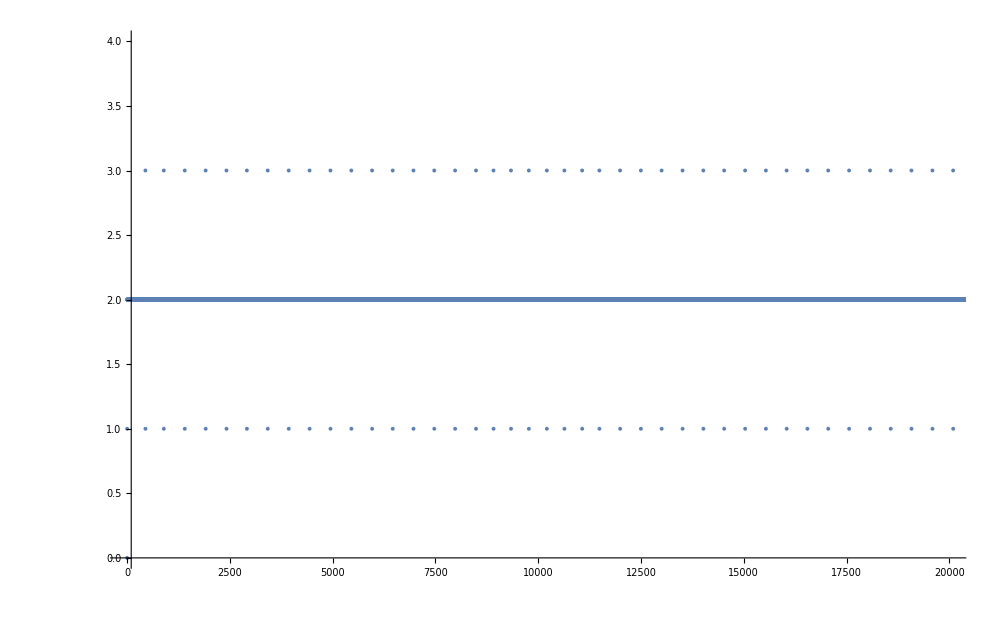

```mathematica
ListPlot[data[[All,1]], PlotRange->{{1,20000},All}]
```

```mathematica
Manipulate[
GraphicsRow[{
ListLinePlot[
	{Select[data2, #[[1]][[1]] ==2& ][[gcrun]][[All,{2,dataset}]]
}
	, PlotLabel ->values[[dataset]]
, PlotRange->All
, ImageSize->Medium
]
,Column[{"gcrun: "<>ToString[gcrun],"data2 index: "<>ToString[gcrun*3],"Length data2[[i]]: "<>ToString[Length[data2[[gcrun*3]]]]}]
,ListLinePlot[
	data2[[gcrun*3]][[All,{2,dataset}]]
	, PlotLabel ->values[[dataset]]
, PlotRange->All
, ImageSize->Medium
]
}]
	,{{gcrun,1,"GC Run"},1, Length[d1],1}
	,{{dataset,11, "Dataset"},1,18,1}
]
```

```mathematica
Dynamic[i]=114
```

Set::write: Tag Dynamic in  is Protected.

```mathematica
i =111
```

111

```mathematica
Column[{Dynamic[ListPlot[data2[[i]][[All,11]],PlotRange->All]],Dynamic[Row[{data2[[i-1,1,1]],":", data2[[i+1,1,1]]}]]}, Frame->All]
```

Delete wrong data:

First identify index of wrong data

Delete wrong data:

```mathematica
i =111+3
```

114

```mathematica
data2[[{i-1,i,i+1}]]=Nothing
```

Nothing

```mathematica
data2[[38]]
```

{{3,2350.1,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}}

Check that data was deleted

```mathematica
data2[[109*3+1+2]][[-12;;-1]]
```

{{2,12.543,304.292,339.084,5.62898,6.11005,2.03211×10^7,-818256.,623.975,631.091,0.051535,629.374,-0.0122833,2.0265×10^7,2.76769×10^7,653.15,653.15,623.15},{2,12.565,304.293,339.085,5.62948,6.1097,2.03214×10^7,-818565.,624.021,631.109,0.0514587,629.225,-0.012323,2.0265×10^7,2.76769×10^7,653.15,653.15,623.15},{2,12.588,304.294,339.097,5.62956,6.11065,2.03207×10^7,-817978.,624.073,631.129,0.0513306,629.371,-0.0124054,2.0265×10^7,2.76769×10^7,653.15,653.15,623.15},{2,12.61,304.293,339.077,5.63014,6.10977,2.03209×10^7,-817792.,624.078,631.125,0.0511719,629.117,-0.0124908,2.0265×10^7,2.76769×10^7,653.15,653.15,623.15},{2,12.636,304.292,339.096,5.5837,6.05612,2.03232×10^7,-815319.,624.035,631.075,0.051297,628.567,-0.0121246,2.0265×10^7,2.76769×10^7,653.15,653.15,623.15},{2,12.658,304.291,339.077,5.55763,6.03091,2.03235×10^7,-816463.,624.128,631.165,0.0512878,629.088,-0.0122833,2.0265×10^7,2.76769×10^7,653.15,653.15,623.15},{2,12.681,304.291,339.077,5.55432,6.02879,2.03216×10^7,-816958.,624.1,631.165,0.0511505,629.339,-0.0126221,2.0265×10^7,2.76769×10^7,653.15,653.15,623.15},{2,12.713,304.295,339.077,5.55583,6.0275,2.03211×10^7,-815350.,624.128,631.153,0.0510529,628.84,-0.012735,2.0265×10^7,2.76769×10^7,653.15,653.15,623.15},{2,12.735,304.293,339.101,5.53895,6.01089,2.0324×10^7,-815195.,624.152,631.109,0.0510132,629.129,-0.0126862,2.0265×10^7,2.76769×10^7,653.15,653.15,623.15},{2,12.758,304.293,339.094,5.53032,6.00199,2.03235×10^7,-815597.,624.228,631.211,0.0510376,629.21,-0.0126617,2.0265×10^7,2.76769×10^7,653.15,653.15,623.15},{2,12.78,304.293,339.102,5.52975,6.00178,2.03237×10^7,-815319.,624.24,631.227,0.0511139,629.28,-0.0128387,2.0265×10^7,2.76769×10^7,653.15,653.15,623.15},{2,12.81,304.292,339.11,5.53023,6.00126,2.03217×10^7,-815350.,624.219,631.232,0.0510315,629.102,-0.0127441,2.0265×10^7,2.76769×10^7,653.15,653.15,623.15}}

```mathematica
Drop[data2, {42*3+1+2,
```

Examine data in relation with temperature:

```mathematica
Manipulate[
Show[
ListPlot[
Select[data2, #[[1]][[1]] ==2& ][[gcrun]][[All,{2,dataset}]]
, PlotLabel ->values[[dataset]]
,PlotRange->{{0,12},{200,700}}
,AxesLabel->{"Time (s)"}
, Joined->True
](* Ends ListPlot*)
, Plot[{-25+273,t*8000./60.-25+273, 60+2000./60*(t-0.6)+273,350+273},{t,0,12}]
, ImageSize->Large
]
,{{gcrun,1,"GC Run"},1, Length[d1],1}
,{{dataset,18, "Dataset"},1,18,1}
] (* Ends Manipulate *)
```

## Plot the data

Print an SFC time to see if it looks sane

```mathematica
d1[[1]]
```

2220.

Create 3D values {t_r1,t_r2,det}

```mathematica
Clear[f]
```

```mathematica
f[x_, y_]:= {Map[Prepend[#,x]&,y]}
```

The number of GC runs:

```mathematica
Select[data2, #[[1]][[1]] ==2& ][[All, All,{2,11}]]//Length
```

258

```mathematica
Length[d1]
```

258

```mathematica
data2d =Inner[f, d1, Select[data2, #[[1]][[1]] ==2& ][[All, All,{2,11}]], Join];
```

```mathematica
params //TableForm
```

GC column description:	Rxi-5Sil MS 0.250 mm x 1 m
SFC flow rate:	0.800
SFC temperature:	22.000
GC flow rate: 	99.000
Experiment title: 	Diesl PAH FAMEs
Sample name: 	7% FAMEs in diesel Total 50 ppm
Analysis type: 	Standard
Concentration: 	9999.000
Operator name: 	DM
Detector sensitivity: 	1.0E-8
FID H2 flow rate: 	36.700
FID Air flow rate: 	300.000
SFC pressure: 	20265000 Pa
SFC dead time: 	2220.000 s
File name: 	C:\SFC-GC\Data\2020_02_29-184604.dat
SFC gradient0:
Rate: 	0 $1 s^-1
Final:	0.000000 $1
Time:	3600.000 s
GC gradient0:
Rate: 	0 $1 s^-1
Final:	243.150000 $1
Time:	0.000 s
GC gradient1:
Rate: 	133 $1 s^-1
Final:	298.150000 $1
Time:	0.000 s
GC gradient2:
Rate: 	33 $1 s^-1
Final:	623.150000 $1
Time:	2.000 s
GC idle temperature:	323.100000 Cdeg
GC purge temperature: 	473.150000 Cdeg
GC sampling temperature: 	243.150000 Cdeg
GC sampling time: 	10
GC load time: 	3
GC vent time: 	2

```mathematica
plot3d = ListPlot3D[
Flatten[data2d,1]
,PlotRange->{All, All, All}
,AxesLabel->{"SFC (s)", "GC (s)","Detector (V)"}
,PlotLabel->StringSplit[params[[6]], ":"][[2]]
,Mesh -> None

(*, ColorFunction->"BlueGreenYellow"*)
]
```

-Graphics3D-

```mathematica
EmitSound[Sound[SoundNote[]]]
```

```mathematica
1040/60.
```

17.3333

```mathematica
17.5*60
```

1050.

```mathematica
Show[plot3d, PlotRange->{All,All,{0,2}}, PlotLabel -> "FAMEs Salmon Oil" ,ImageSize->Full]
```

-Graphics3D-

```mathematica
Show[plot3d, PlotRange->{{2200,3600},All,{0,6}}, ImageSize-> Full]
```

-Graphics3D-

```mathematica
Slider[Dynamic[opac]]
```

```mathematica
color = Dynamic[RGBColor[1,0,0,.5]]
```

```mathematica
Dynamic[i]
```

```mathematica
i=50
```

50

```mathematica
Slider[Dynamic[i],{1,Length[data2d],1}]
```

```mathematica
Show[plot3d, Graphics3D[{color,Line[data2d],Opacity[1], Black, Dynamic[Line[data2d[[i]]]]}],PlotRange->{All,All,{0,3}}, ImageSize->Full]
```

-Graphics3D-

Make a virtual SFC Chromatogram:

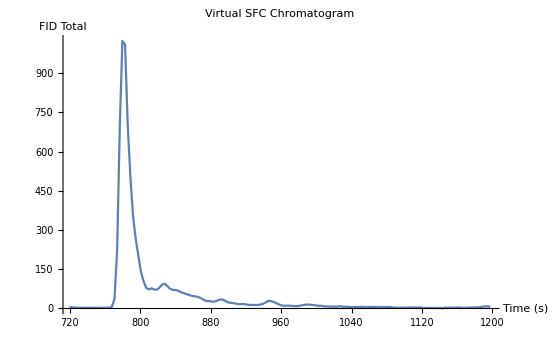

```mathematica
ListLinePlot[Partition[Riffle[d1,(Total[#]&/@data2d)[[All,3]]],2], PlotLabel->"Virtual SFC Chromatogram", AxesLabel->{"Time (s)","FID Total"}, PlotRange->{All, All}]
```

Create graphics for export to the thesis or publication:

```mathematica
exportgraphic = Show[
	plot3d
	,PlotLabel -> Style["FAMEs: Canola oil", Large, Bold, Black]
	, AxesStyle -> {Directive[Black, Bold, 15]
				, Directive[Black, Bold, 15]
				, Directive[Black, Bold, 15]
				}
	,AxesLabel-> 
		{Style["SFC (s)", Large, Bold, Black]
		, Style[ "GC (s)",Large, Bold, Black]
		,Style[Rotate["Detector (V)", 90 Degree], Large, Bold, Black]
		}
	(*, ViewPoint->{10000,10000,10000} *)
	, ImageSize-> 1024
	, ViewPoint->vp
	
]
```

```mathematica
Export["C:\\Users\\fskdm\\My PhD\\Conferences\\Analitika 2018\\Poster\\images\\Canola.png",exportgraphic,Background->None, ViewPoint->vp]
```

C:\Users\fskdm\My PhD\Conferences\Analitika 2018\Poster\images\Canola.png

```mathematica
Show[
	plot3d
(*	,Graphics3D[{Red,Line[data2d]}] *)
     , PlotLabel -> "Mystery Oil"
	, PlotRange-> {All, All,{0,0.1}}
]
```

```mathematica
contourplot =ListContourPlot[Flatten[data2d,1], PlotRange->{{700,1200}, All, {0,1}}, AxesLabel->{"SFC (s)", "GC (s)"}, ImageSize->Full]
```

-Graphics-

```mathematica
Show[contourplot, PlotRange->{All, All}, ImageSize-> Full]
```

-Graphics-